```mathematica
inicial = {0,0,0,1,0,0,1,0,1,0};
inicial2 = {0,0,1,0,1,1,1,0,0,1,1,1,0,0,1,0,1,0,0,1};
inicial3 = {0,0,1,0,1,1,1,0,0,1,1,1,0,0,1,0,1,0,0,1,1,1,1,0,0,1,0,1,0,0,1,1,0,1,0,1,0,1,0,1};
regla2 = 22;
regla = 54;
t = 2;
AC[Inicial_List, Regla_Integer, t_Integer]:=Module[{reglaN, lista={},i,j,seed, listaAux={}, aux,index0,index1,index2},
lista = Append[lista,Inicial];
seed = Inicial;
reglaN = BinarizacionDeReglas[Regla];
For[i=1, i≤ t,i++,
listaAux = {};
For[j=1, j≤ Length[seed],j++,
aux = {};
If[j-1 == 0,
index0 = -1;(* -1 = ultimo elemento*)
,(*else*)
index0 =  Mod[j-1,Length[seed]+1];
];(*if parte izquierda*)
index1 = Mod[j,Length[seed]+1];
If[j==Length[seed],
index2 = 1;
,(*else*)
index2 = Mod[j+1,Length[seed]+1];
];(*If parte derecha*)
aux=Append[aux,seed[[index0]]];
aux=Append[aux,seed[[index1]]];
aux=Append[aux,seed[[index2]]];
(*{0,1,0,_}*)
aux = Append[aux,_];

aux = Cases[reglaN,aux];
aux = aux[[1]][[4]]; (*Cogemos el ultimo elemento = 0,1,0 -> 1*)
listaAux = Append[listaAux,aux]; (*proximo seed, es el resultado*)
];(*Fin for j*)
lista = Append[lista,listaAux];
seed = listaAux;


];(*Fin for i*)

ArrayPlot[lista];
Return[lista];
]
```

```mathematica
BinarizacionDeReglas[N_Integer]:=Module[{List={},binario,i,auxBin},

binario = FormateoBinarioReversed[N,8];

For[i=0,i<8,i++,
auxBin = Reverse[FormateoBinarioReversed[i,3]];
auxBin = Append[auxBin,binario[[i+1]]];
List = Append[List,auxBin];
];(*Fin for*)
Return[List];
];
```

```mathematica
FormateoBinarioReversed[N_Integer,Long_Integer]:=Module[{i, binario},
binario = Reverse[IntegerDigits[N,2]];
For[i=Length[binario],i<Long,i++,
binario = Append[binario,0];
];
Return[binario];
];
```

```mathematica
AC[inicial3,124,50]
```

{{0,0,1,0,1,1,1,0,0,1,1,1,0,0,1,0,1,0,0,1,1,1,1,0,0,1,0,1,0,0,1,1,0,1,0,1,0,1,0,1},{1,0,1,1,1,0,1,1,0,1,0,1,1,0,1,1,1,1,0,1,0,0,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,0,1,1,1,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,1,0,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{1,1,1,0,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,0,1,0,1,1,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,0,0,0,0,0,0,0,1,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{1,1,1,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0},{1,0,1,1,0,0,1,1,1,0,0,0,0,0,1,1,1,0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,1,0,1,1,0,0,0,0},{1,1,1,1,1,0,1,0,1,1,0,0,0,0,1,0,1,1,1,1,1,0,0,0,0,1,0,1,1,0,0,0,1,1,1,1,1,0,0,0},{1,0,0,0,1,1,1,1,1,1,1,0,0,0,1,1,1,0,0,0,1,1,0,0,0,1,1,1,1,1,0,0,1,0,0,0,1,1,0,0},{1,1,0,0,1,0,0,0,0,0,1,1,0,0,1,0,1,1,0,0,1,1,1,0,0,1,0,0,0,1,1,0,1,1,0,0,1,1,1,0},{1,1,1,0,1,1,0,0,0,0,1,1,1,0,1,1,1,1,1,0,1,0,1,1,0,1,1,0,0,1,1,1,1,1,1,0,1,0,1,1},{0,0,1,1,1,1,1,0,0,0,1,0,1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,1,1,1,1,1,0},{0,0,1,0,0,0,1,1,0,0,1,1,1,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,1,0,0,0,1,1},{1,0,1,1,0,0,1,1,1,0,1,0,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,1,0,0,1,1},{1,1,1,1,1,0,1,0,1,1,1,1,1,0,0,0,1,1,1,1,1,0,0,0,0,0,0,1,1,0,1,1,1,0,1,1,1,0,1,0},{1,0,0,0,1,1,1,1,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,0,0,0,1,1,1,1,0,1,1,1,0,1,1,1,1},{1,1,0,0,1,0,0,0,1,1,0,0,1,1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,0,0,1,1,1,0,1,1,1,0,0,0},{1,1,1,0,1,1,0,0,1,1,1,0,1,0,1,1,1,1,1,0,1,0,1,1,0,0,0,1,1,0,1,0,1,1,1,0,1,1,0,0},{1,0,1,1,1,1,1,0,1,0,1,1,1,1,1,0,0,0,1,1,1,1,1,1,1,0,0,1,1,1,1,1,1,0,1,1,1,1,1,0},{1,1,1,0,0,0,1,1,1,1,1,0,0,0,1,1,0,0,1,0,0,0,0,0,1,1,0,1,0,0,0,0,1,1,1,0,0,0,1,1},{0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,1,1,0,1,1,0,0,0,0,1,1,1,1,1,0,0,0,1,0,1,1,0,0,1,0},{0,0,1,1,1,0,1,1,0,0,1,1,1,0,1,0,1,1,1,1,1,0,0,0,1,0,0,0,1,1,0,0,1,1,1,1,1,0,1,1},{1,0,1,0,1,1,1,1,1,0,1,0,1,1,1,1,1,0,0,0,1,1,0,0,1,1,0,0,1,1,1,0,1,0,0,0,1,1,1,1},{1,1,1,1,1,0,0,0,1,1,1,1,1,0,0,0,1,1,0,0,1,1,1,0,1,1,1,0,1,0,1,1,1,1,0,0,1,0,0,0},{1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,1,1,0,1,0,1,1,1,0,1,1,1,1,1,0,0,1,1,0,1,1,0,0},{1,1,0,0,1,1,1,0,1,1,0,0,1,1,1,0,1,0,1,1,1,1,1,0,1,1,1,0,0,0,1,1,0,1,1,1,1,1,1,0},{1,1,1,0,1,0,1,1,1,1,1,0,1,0,1,1,1,1,1,0,0,0,1,1,1,0,1,1,0,0,1,1,1,1,0,0,0,0,1,1},{0,0,1,1,1,1,1,0,0,0,1,1,1,1,1,0,0,0,1,1,0,0,1,0,1,1,1,1,1,0,1,0,0,1,1,0,0,0,1,0},{0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,1,1,0,1,1,1,0,0,0,1,1,1,1,0,1,1,1,0,0,1,1},{1,0,1,1,0,0,1,1,1,0,1,1,0,0,1,1,1,0,1,0,1,1,1,0,1,1,0,0,1,0,0,1,1,1,0,1,1,0,1,1},{1,1,1,1,1,0,1,0,1,1,1,1,1,0,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,0,1,0,1,1,1,1,1,1,0},{1,0,0,0,1,1,1,1,1,0,0,0,1,1,1,1,1,0,0,0,1,1,1,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,1,1},{1,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,1,1,0,0,1,0,0,0,0,0,0,1,1,0,0,0,1,0},{1,1,1,0,1,1,0,0,1,1,1,0,1,1,0,0,1,1,1,0,1,1,1,1,1,0,1,1,0,0,0,0,0,1,1,1,0,0,1,1},{0,0,1,1,1,1,1,0,1,0,1,1,1,1,1,0,1,0,1,1,1,0,0,0,1,1,1,1,1,0,0,0,0,1,0,1,1,0,1,0},{0,0,1,0,0,0,1,1,1,1,1,0,0,0,1,1,1,1,1,0,1,1,0,0,1,0,0,0,1,1,0,0,0,1,1,1,1,1,1,1},{1,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,1,1,1,1,0,1,1,0,0,1,1,1,0,0,1,0,0,0,0,0,1},{1,1,1,1,1,0,1,1,0,0,1,1,1,0,1,1,0,0,1,0,0,0,1,1,1,1,1,0,1,0,1,1,0,1,1,0,0,0,0,1},{0,0,0,0,1,1,1,1,1,0,1,0,1,1,1,1,1,0,1,1,0,0,1,0,0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,1},{1,0,0,0,1,0,0,0,1,1,1,1,1,0,0,0,1,1,1,1,1,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,1},{1,1,0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,1,1,1,0,1},{0,1,1,0,1,1,1,0,1,1,0,0,1,1,1,0,1,1,0,0,1,0,0,0,1,1,1,1,1,0,0,0,0,0,0,1,0,1,1,1},{1,1,1,1,1,0,1,1,1,1,1,0,1,0,1,1,1,1,1,0,1,1,0,0,1,0,0,0,1,1,0,0,0,0,0,1,1,1,0,1},{0,0,0,0,1,1,1,0,0,0,1,1,1,1,1,0,0,0,1,1,1,1,1,0,1,1,0,0,1,1,1,0,0,0,0,1,0,1,1,1},{1,0,0,0,1,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,1,1,1,1,0,1,0,1,1,0,0,0,1,1,1,0,1},{1,1,0,0,1,1,1,1,1,0,1,1,0,0,1,1,1,0,1,1,0,0,1,0,0,0,1,1,1,1,1,1,1,0,0,1,0,1,1,1},{0,1,1,0,1,0,0,0,1,1,1,1,1,0,1,0,1,1,1,1,1,0,1,1,0,0,1,0,0,0,0,0,1,1,0,1,1,1,0,0},{0,1,1,1,1,1,0,0,1,0,0,0,1,1,1,1,1,0,0,0,1,1,1,1,1,0,1,1,0,0,0,0,1,1,1,1,0,1,1,0},{0,1,0,0,0,1,1,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,1,1,1,1,0,0,0,1,0,0,1,1,1,1,1},{1,1,1,0,0,1,1,1,1,1,1,0,1,1,0,0,1,1,1,0,1,1,0,0,1,0,0,0,1,1,0,0,1,1,0,1,0,0,0,1}}

```mathematica
ArrayPlot[%91]
```

-Graphics-

```mathematica
ArrayPlot[%8]
```

```mathematica
ArrayPlot[%70]
```

-Graphics-

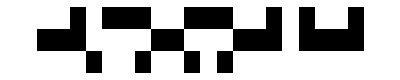

```mathematica
ArrayPlot[{{0,0,1,0,1,1,1,0,0,1,1,1,0,0,1,0,1,0,0,1},{1,1,1,0,0,0,0,1,1,0,0,0,1,1,1,0,1,1,1,1},{0,0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0}}]
```

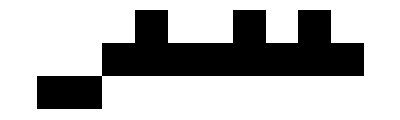

```mathematica
ArrayPlot[{{0,0,0,1,0,0,1,0,1,0},{0,0,1,1,1,1,1,1,1,1},{1,1,0,0,0,0,0,0,0,0}}]
```